```mathematica
Quit[]
```

## Load Model and Compute Diagrams

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
$FCVerbose=0;
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
$FAVerbose=0;
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;

(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../../FA_models/SMS-stop-SMQCD-NLO_FA",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
```

The choice below for the momenta and the ordering of the particles in the process is equivalent to the correct
ordering for computing the effective vertex for the UFO format:
0 →3, with {} →{-F[9],F[9],V[4]} and all the momenta set as outgoing ({} → {p1,p2,p3}).
However the choice below produces nicer diagrams.

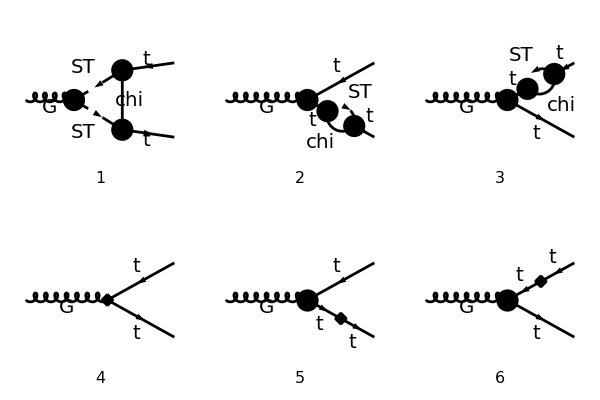

```mathematica
topsCT = CreateCTTopologies[1,1->2];
tops = CreateTopologies[1,1->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles}];
processGGT =  {V[1]}->  {-F[3],F[3]};
allDiags = InsertFields[Join[tops,topsCT],processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[1],V[2],V[3]}];
goodDiags=allDiags;
Paint[goodDiags,ColumnsXRows->{3,2},ImageSize->{ 600,400},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

## Compute Amplitude

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT},IncomingMomenta->{p3},OutgoingMomenta->{-p1,-p2},LoopMomenta->{q},List->False,SUNIndexNames->{cc3,aa,bb},SUNFIndexNames->{a,c1,c2},DropSumOver->True,LorentzIndexNames->{ μ}, SMP->True,List->False,Contract->True,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings/.GS->gs)]/.{GS->gs,FR$deltaZ[{G,G},{{}}]->deltaZG,FR$deltaZ[{t,t},{{}},"L"]->deltaZL,FR$deltaZ[{t,t},{{}},"R"]->deltaZR,FR$delta[{MT},{}]->deltaM,FR$delta[{aS},{}]->deltaaS};
ampB =FullSimplify[SUNSimplify[DiracSimplify[FCReplaceMomenta[ampA,{p3->-p1-p2}]]]];
```

Simplify counter-terms (see top_SelfEnergy_CT.nb and top-Vertex_CT.nb):
(since we assume MT < mChi + MT, B1[MT^2] is always real)

```mathematica
CTsubs={deltaZG->0,deltaaS->0,deltaZL -> Pi^2yDM^2  MT^2  Re[DB1[MT^2,mChi^2,mST^2,BReduce->False]],deltaZR-> Pi^2  yDM^2( MT^2 Re[DB1[MT^2,mChi^2,mST^2,BReduce->False]]+PaVe[1,{MT^2},{mChi^2,mST^2},PaVeAutoOrder->False,PaVeAutoReduce->False]),deltaM->-Pi^2/2 yDM^2 MT PaVe[1,{MT^2},{mChi^2,mST^2},PaVeAutoOrder->False,PaVeAutoReduce->False]};
ampB2=ampB/.CTsubs;
```

Evaluate Loop integrals:

```mathematica
ampC =FCCanonicalizeDummyIndices[( TID[ampB2,q,UsePaVeBasis->True,PaVeAutoReduce->False,ToPaVe->True,PaVeAutoOrder->False]//Simplify),LorentzIndexNames-> {μ,ν}];
```

```mathematica
FCClearScalarProducts[];
SPD[p1,p2]=1/2(SPD[p3,p3]-SPD[p1,p1]-SPD[p2,p2]);
ampD=FullSimplify[DiracSimplify[ampC]];
ampEsimp2=Simplify[(ExpandScalarProduct[DiracSimplify[ampD]])];
```

## Check Divergences (note that the DB1 loop integral is finite)

```mathematica
lInts = Cases2[ampEsimp2,{A0,B0,C0,D0,B1,DB1,PaVe}];
lIntsUV=Table[lInt->PaXEvaluateUV[lInt,PaXImplicitPrefactor->1/(2 Pi)^4],{lInt,lInts}];
lIntsUV//MatrixForm
```

PaXEvaluate::convFail: Warning! Not all scalar loop integrals in the expression could be prepared to be processed with Package X. Following integrals will not be handled by Package X: {DB1(MT^2,mChi^2,mST^2,BReduce→False)}

(DB1(MT^2,mChi^2,mST^2,BReduce→False)→0
B_1(MT^2,mChi^2,mST^2)→-1/(32 π^4 ε_UV)
B_1(p1^2,mChi^2,mST^2)→-1/(32 π^4 ε_UV)
B_1(p2^2,mChi^2,mST^2)→-1/(32 π^4 ε_UV)
C_1(p1^2,p3^2,p2^2,mChi^2,mST^2,mST^2)→0
C_2(p1^2,p3^2,p2^2,mChi^2,mST^2,mST^2)→0
C_00(p1^2,p3^2,p2^2,mChi^2,mST^2,mST^2)→1/(64 π^4 ε_UV)
C_11(p1^2,p3^2,p2^2,mChi^2,mST^2,mST^2)→0
C_12(p1^2,p3^2,p2^2,mChi^2,mST^2,mST^2)→0
C_22(p1^2,p3^2,p2^2,mChi^2,mST^2,mST^2)→0)

```mathematica
loopUV=FullSimplify[ampEsimp2/.lIntsUV]
```

0

## Simplify Result

```mathematica
ampEsimp3a=Simplify[DiracSimplify[FeynAmpDenominatorExplicit[ampEsimp2]]];
```

### Order PaVe integrals (note that B1 and DB1 are already ordered as B1[x] = B1[x,mChi^2,mST^2] and DB1[x] = DB1[x,mChi^2,mST^2])

```mathematica
lInts = Cases2[ampEsimp3a,{A0,B0,C0,B1,D0,PaVe}];
orderedPaVes=Table[lInt->PaVeOrder[lInt,PaVeOrderList->{Pair[Momentum[p2,D],Momentum[p2,D]],mChi^2,mST^2,mST^2},Sum->True],{lInt,lInts}];
ampEsimp4=ampEsimp3a/.orderedPaVes;
lIntsOrdered = Cases2[ampEsimp4,{A0,B0,C0,D0,B1,DB1,PaVe}];
lIntsOrdered//MatrixForm
```

(DB1(MT^2,mChi^2,mST^2,BReduce→False)
B_1(MT^2,mChi^2,mST^2)
B_1(p1^2,mChi^2,mST^2)
B_1(p2^2,mChi^2,mST^2)
C_1(p1^2,p3^2,p2^2,mChi^2,mST^2,mST^2)
C_2(p1^2,p3^2,p2^2,mChi^2,mST^2,mST^2)
C_00(p1^2,p3^2,p2^2,mChi^2,mST^2,mST^2)
C_11(p1^2,p3^2,p2^2,mChi^2,mST^2,mST^2)
C_12(p1^2,p3^2,p2^2,mChi^2,mST^2,mST^2)
C_22(p1^2,p3^2,p2^2,mChi^2,mST^2,mST^2))

### Make propagators explicit

```mathematica
ampEsimp5=FeynAmpDenominatorExplicit[DiracSimplify[ampEsimp4]];
```

## Extract Color and Lorentz (Tensor) Structure

First group terms by number of gamma matrices and momenta

```mathematica
spinorChains=DeleteDuplicates@Select[Cases[ampEsimp5,_Dot,Infinity],VectorQ[List@@#,MatchQ[#,_DiracGamma]&]&];
singleGamma=DeleteDuplicates@Cases[Select[ampEsimp5,Count[#,_DiracGamma,Infinity]==1&],_DiracGamma,All];
diracStructures=Sort[DeleteDuplicates@Join[singleGamma,spinorChains]]
momentumStructures=Sort[Join[{1},Cases2[ampEsimp5,Pair,All]]];
(* Remove appearances of pi^2, since they do not contribute to the tensor structure*)
momentumStructures=DeleteCases[momentumStructures,Pair[Momentum[a_,___],Momentum[a_,___]],All]
colorStructures = Sort[Join[Cases2[ampEsimp5,SUNTF],Cases2[ampEsimp5,SUNF]]]
```

{γ^μ,γ^μ.(γ̄)^6,γ^μ.(γ̄)^7,γ^μ.(γ·p1),(γ·p1).(γ̄)^6,(γ·p2).(γ̄)^6,(γ·p2).γ^μ,γ^μ.(γ·p1).(γ̄)^6,γ^μ.(γ·p1).(γ̄)^7,(γ·p2).γ^μ.(γ̄)^6,(γ·p2).γ^μ.(γ̄)^7}

{1,p1^μ,p2^μ}

{T_c2c1^cc3}

Some additional simplifications (replace γ^μ->γ^μ γ^6+γ^μ γ^7 in three terms):

```mathematica
hasgQ[n_]:=Count[#,DiracGamma[n,D],All]==1&;
hasgmuQ=Count[#,DiracGamma[LorentzIndex[μ,D],D],All]==1&;
haspQ[p_]:=Count[#,Momentum[p,D],All]==1&;
first[list_,pred_]:=FirstCase[list,_?pred];
subsets=<|gmu->Select[diracStructures,!haspQ[p1][#]&&!haspQ[p2][#]&&hasgmuQ[#]&],p1gmu->Select[diracStructures,haspQ[p1][#]&&!haspQ[p2][#]&&hasgmuQ[#]&],p2gmu->Select[diracStructures,!haspQ[p1][#]&&haspQ[p2][#]&&hasgmuQ[#]&]|>;
rules=KeyValueMap[Function[{lhs,list},{first[list,!hasgQ[6][#]&&!hasgQ[7][#]&],first[list,hasgQ[6]]+first[list,hasgQ[7]]}],subsets]
```

(γ^μ | γ^μ.(γ̄)^6+γ^μ.(γ̄)^7
γ^μ.(γ·p1) | γ^μ.(γ·p1).(γ̄)^6+γ^μ.(γ·p1).(γ̄)^7
(γ·p2).γ^μ | (γ·p2).γ^μ.(γ̄)^6+(γ·p2).γ^μ.(γ̄)^7)

```mathematica
ampEsimp6=ampEsimp5;
Do[
diracStructure=dirRep[[1]];
diracRep=dirRep[[2]];
coeff=Coefficient[Expand[ampEsimp6],diracStructure];
ampEsimp6=Simplify[ampEsimp6-coeff*diracStructure]+Expand[coeff*diracRep],
{dirRep,rules}
]
```

### Split terms according to the tensor structure and color structure and factor out the vertex coupling

```mathematica
couplingTerms=DeleteDuplicates[(gs^Exponent[#,gs] yDM^Exponent[#,yDM])&/@List@@Expand[ampEsimp6]];
globalFactor = I Pi^2;
structTerms = Select[Flatten[KroneckerProduct[diracStructures,momentumStructures]],Count[#,LorentzIndex[μ,D],Infinity]==1&];
coefficients=Join@@Join@@Table[{coupling*globalFactor,colorStructure,structure,Collect[Expand[FullSimplify[Coefficient[Coefficient[Coefficient[Expand[ampEsimp6/globalFactor],coupling],colorStructure],structure]]],{_C00,_B1,_Re},FullSimplify]},{structure,structTerms},{colorStructure,colorStructures},{coupling,couplingTerms}];
(* Select only non-zero coefficients *)
coefficients=Select[coefficients,#[[-1]]=!=0&]
```

(ⅈ π^2 gs yDM^2 | T_c2c1^cc3 | γ^μ.(γ̄)^6 | (2 (MT^2-p1^2) (MT^2-p2^2) C_00(p1^2,p3^2,p2^2,mChi^2,mST^2,mST^2)+MT^2 (-p1^2) B_1(p1^2,mChi^2,mST^2)-MT^2 p2^2 B_1(p2^2,mChi^2,mST^2)+(MT^4-p1^2 p2^2) B_1(MT^2,mChi^2,mST^2)+p1^2 p2^2 B_1(p1^2,mChi^2,mST^2)+p1^2 p2^2 B_1(p2^2,mChi^2,mST^2))/((MT^2-p1^2) (MT^2-p2^2))-MT^2 Re(DB1(MT^2,mChi^2,mST^2,BReduce→False))
ⅈ π^2 gs yDM^2 | T_c2c1^cc3 | γ^μ.(γ̄)^7 | -MT^2 Re(DB1(MT^2,mChi^2,mST^2,BReduce→False))
ⅈ π^2 gs yDM^2 | T_c2c1^cc3 | p1^μ (γ·p1).(γ̄)^6 | C_1(p1^2,p3^2,p2^2,mChi^2,mST^2,mST^2)+2 C_11(p1^2,p3^2,p2^2,mChi^2,mST^2,mST^2)
ⅈ π^2 gs yDM^2 | T_c2c1^cc3 | p2^μ (γ·p1).(γ̄)^6 | -C_1(p1^2,p3^2,p2^2,mChi^2,mST^2,mST^2)-2 C_12(p1^2,p3^2,p2^2,mChi^2,mST^2,mST^2)
ⅈ π^2 gs yDM^2 | T_c2c1^cc3 | p1^μ (γ·p2).(γ̄)^6 | -2 C_12(p1^2,p3^2,p2^2,mChi^2,mST^2,mST^2)-C_2(p1^2,p3^2,p2^2,mChi^2,mST^2,mST^2)
ⅈ π^2 gs yDM^2 | T_c2c1^cc3 | p2^μ (γ·p2).(γ̄)^6 | C_2(p1^2,p3^2,p2^2,mChi^2,mST^2,mST^2)+2 C_22(p1^2,p3^2,p2^2,mChi^2,mST^2,mST^2)
ⅈ π^2 gs yDM^2 | T_c2c1^cc3 | γ^μ.(γ·p1).(γ̄)^6 | (MT (B_1(MT^2,mChi^2,mST^2)-B_1(p1^2,mChi^2,mST^2)))/(MT^2-p1^2)
ⅈ π^2 gs yDM^2 | T_c2c1^cc3 | (γ·p2).γ^μ.(γ̄)^7 | (MT (B_1(p2^2,mChi^2,mST^2)-B_1(MT^2,mChi^2,mST^2)))/(MT^2-p2^2))

Check that the coefficients really give the full result

```mathematica
ampTot =Sum[Times@@c,{c,coefficients}];
Simplify[ampTot-ampEsimp6]
```

0

## Define UV finite loop functions and convert to collier notation the finite integrals (only the normalized/UV finite functions should appear in the final result)

```mathematica
Needs["PaVeToCollierConverter`"]
```

```mathematica
loopFunctionsHat={PaVe[1,{Pair[x1___]},{mChi^2,mST^2},opt___]->B1h[Pair[x1]]+PaVe[1,{MT^2},{mChi^2,mST^2},opt],
PaVe[0,0,{x1_,x2_,x3_},{mChi^2,mST^2,mST^2},opt___]->C00h[x1,x2,x3]-1/2 PaVe[1,{MT^2},{mChi^2,mST^2},opt],Re[DB1[MT^2,mChi^2,mST^2,___]]->reDB1[MT^2]};
convert2Collier=Table[lInt->PaVeToCollier[lInt,MassList->{mChi^2,mST^2,mST^2}],{lInt,lIntsOrdered[[5;;]]}];
```

```mathematica
coefficientsH=FullSimplify[coefficients/.loopFunctionsHat/.convert2Collier]
```

(ⅈ π^2 gs yDM^2 | T_c2c1^cc3 | γ^μ.(γ̄)^6 | 2 C00h(p1^2,p3^2,p2^2)-(p1^2 B1h(p1^2))/(MT^2-p1^2)-(p2^2 B1h(p2^2))/(MT^2-p2^2)+MT^2 (-reDB1(MT^2))
ⅈ π^2 gs yDM^2 | T_c2c1^cc3 | γ^μ.(γ̄)^7 | -MT^2 reDB1(MT^2)
ⅈ π^2 gs yDM^2 | T_c2c1^cc3 | p1^μ (γ·p1).(γ̄)^6 | Ccoll(0,1,0,p1^2,p3^2,p2^2)+2 Ccoll(0,2,0,p1^2,p3^2,p2^2)
ⅈ π^2 gs yDM^2 | T_c2c1^cc3 | p2^μ (γ·p1).(γ̄)^6 | -Ccoll(0,1,0,p1^2,p3^2,p2^2)-2 Ccoll(0,1,1,p1^2,p3^2,p2^2)
ⅈ π^2 gs yDM^2 | T_c2c1^cc3 | p1^μ (γ·p2).(γ̄)^6 | -Ccoll(0,0,1,p1^2,p3^2,p2^2)-2 Ccoll(0,1,1,p1^2,p3^2,p2^2)
ⅈ π^2 gs yDM^2 | T_c2c1^cc3 | p2^μ (γ·p2).(γ̄)^6 | Ccoll(0,0,1,p1^2,p3^2,p2^2)+2 Ccoll(0,0,2,p1^2,p3^2,p2^2)
ⅈ π^2 gs yDM^2 | T_c2c1^cc3 | γ^μ.(γ·p1).(γ̄)^6 | (MT B1h(p1^2))/(p1^2-MT^2)
ⅈ π^2 gs yDM^2 | T_c2c1^cc3 | (γ·p2).γ^μ.(γ̄)^7 | (MT B1h(p2^2))/(MT^2-p2^2))

#### On - shell Limit:

```mathematica
onShell[coeff_]:=FullSimplify[Normal[Series[coeff/.{MT-> √MT2,Pair[Momentum[p_,___],Momentum[p_,___]]:> ToExpression[ToString[p]<>"sq"]},{p1sq,MT2,0},{p2sq,MT2,0}]]/.{reDB1[MT2]->D[B1h[MT2],MT2],B1h[MT2]->0}];
```

```mathematica
coeffientsOn=Table[Join[coeff[[1;;-2]],{onShell[coeff[[-1]]]}],{coeff,coefficientsH}];
coeffientsOn//MatrixForm
```

(ⅈ π^2 gs yDM^2 | T_c2c1^cc3 | γ^μ.(γ̄)^6 | 2 C00h(MT2,p3sq,MT2)+MT2 B1h'(MT2)
ⅈ π^2 gs yDM^2 | T_c2c1^cc3 | γ^μ.(γ̄)^7 | -MT2 B1h'(MT2)
ⅈ π^2 gs yDM^2 | T_c2c1^cc3 | p1^μ (γ·p1).(γ̄)^6 | Ccoll(0,1,0,MT2,p3sq,MT2)+2 Ccoll(0,2,0,MT2,p3sq,MT2)
ⅈ π^2 gs yDM^2 | T_c2c1^cc3 | p2^μ (γ·p1).(γ̄)^6 | -Ccoll(0,1,0,MT2,p3sq,MT2)-2 Ccoll(0,1,1,MT2,p3sq,MT2)
ⅈ π^2 gs yDM^2 | T_c2c1^cc3 | p1^μ (γ·p2).(γ̄)^6 | -Ccoll(0,0,1,MT2,p3sq,MT2)-2 Ccoll(0,1,1,MT2,p3sq,MT2)
ⅈ π^2 gs yDM^2 | T_c2c1^cc3 | p2^μ (γ·p2).(γ̄)^6 | Ccoll(0,0,1,MT2,p3sq,MT2)+2 Ccoll(0,0,2,MT2,p3sq,MT2)
ⅈ π^2 gs yDM^2 | T_c2c1^cc3 | γ^μ.(γ·p1).(γ̄)^6 | √MT2 B1h'(MT2)
ⅈ π^2 gs yDM^2 | T_c2c1^cc3 | (γ·p2).γ^μ.(γ̄)^7 | -√MT2 B1h'(MT2))

Once we convert the p - slash terms below by + - MT (since they apply to external spinors), the above result reproduces what was obtained in 2312.00670

### Finally, for convenience, define pB1h to artificial numerical divergences : (note that 1/(p^2-MT^2)B1h[p^2]->DB1[MT^2] for p^2-> MT^2, so pB1h[p^2]->DB1h[MT^2] for p^2-> MT^2)

```mathematica
coefficientsHsimp=Simplify[coefficientsH/.{B1h[x1_]->(x1-MT^2)pB1h[x1]}]
```

(ⅈ π^2 gs yDM^2 | T_c2c1^cc3 | γ^μ.(γ̄)^6 | 2 C00h(p1^2,p3^2,p2^2)+MT^2 (-reDB1(MT^2))+p1^2 pB1h(p1^2)+p2^2 pB1h(p2^2)
ⅈ π^2 gs yDM^2 | T_c2c1^cc3 | γ^μ.(γ̄)^7 | -MT^2 reDB1(MT^2)
ⅈ π^2 gs yDM^2 | T_c2c1^cc3 | p1^μ (γ·p1).(γ̄)^6 | Ccoll(0,1,0,p1^2,p3^2,p2^2)+2 Ccoll(0,2,0,p1^2,p3^2,p2^2)
ⅈ π^2 gs yDM^2 | T_c2c1^cc3 | p2^μ (γ·p1).(γ̄)^6 | -Ccoll(0,1,0,p1^2,p3^2,p2^2)-2 Ccoll(0,1,1,p1^2,p3^2,p2^2)
ⅈ π^2 gs yDM^2 | T_c2c1^cc3 | p1^μ (γ·p2).(γ̄)^6 | -Ccoll(0,0,1,p1^2,p3^2,p2^2)-2 Ccoll(0,1,1,p1^2,p3^2,p2^2)
ⅈ π^2 gs yDM^2 | T_c2c1^cc3 | p2^μ (γ·p2).(γ̄)^6 | Ccoll(0,0,1,p1^2,p3^2,p2^2)+2 Ccoll(0,0,2,p1^2,p3^2,p2^2)
ⅈ π^2 gs yDM^2 | T_c2c1^cc3 | γ^μ.(γ·p1).(γ̄)^6 | MT pB1h(p1^2)
ⅈ π^2 gs yDM^2 | T_c2c1^cc3 | (γ·p2).γ^μ.(γ̄)^7 | -MT pB1h(p2^2))

## Check ALOHA convertion

```mathematica
Needs["alohaTranslator`"]
```

UFO conventions:
ProjM -> Gamma[7], ProjP -> Gamma[6]
particles = [ P.t__tilde __, P.t, P.g ] ] = [ p1=P(*,1),  p2=P(*,2), p3(μ)=P(*,3) ] (all momenta are incoming)
c2 = Top color = "2", c1 = Anti-Top color = "1", c3 = Gluon color = "3"
spins = [2, 2, 3], 
structure = ' P (4, 3)*Gamma (3, 2, -1)*ProjP (-1, 1) - P (3, 4)*Gamma (4, 2, -1)*ProjP (-1, 1)')
(The indices of the product of gamma matrices are always M(2,1), since the second (outgoing) top is contracted to the left and the first (incoming) to the right)

### Define relevant input for numbering the ALOHA indices:

```mathematica
gluonIndex=3;
topIndex=2;
antiTopIndex=1;
leftIndex=topIndex;
rightIndex=antiTopIndex;
momentumMap=<|p1->antiTopIndex,p2->topIndex,p3->gluonIndex|>;
lorentzMap=<|μ->gluonIndex|>;
colorMap=<|cc3->gluonIndex,c2->topIndex,c1->antiTopIndex|>;
opts=Sequence@@{MomentumMap->momentumMap,LorentzMap->lorentzMap,ColorMap->colorMap,
LeftIndex->leftIndex,RightIndex->rightIndex};
```

Define additional translations which might be needed:

```mathematica
alohaDispatch[gs]:="G";
alohaDispatch[Pi]:="cmath.pi";
```

### Convert to ALOHA splitting the color and tensor structure:

```mathematica
coefficientsALOHA=Table[Table[alohaTranslator[term,opts],{term,c}],{c,coefficientsHsimp}];
coefficientsALOHA//MatrixForm
```

(complex(0,1)*G*(cmath.pi)**2*(yDM)**2 | T(3,2,1) | Gamma(3,2,-1)*ProjP(-1,1) | -1*(MT)**2*reDB1 + 2*C00h( P(-1,1)*P(-1,1), P(-2,3)*P(-2,3), P(-3,2)*P(-3,2) ) + P(-4,1)*P(-4,1)*pB1h( P(-5,1)*P(-5,1) ) + P(-6,2)*P(-6,2)*pB1h( P(-7,2)*P(-7,2) )
complex(0,1)*G*(cmath.pi)**2*(yDM)**2 | T(3,2,1) | Gamma(3,2,-1)*ProjM(-1,1) | -1*(MT)**2*reDB1
complex(0,1)*G*(cmath.pi)**2*(yDM)**2 | T(3,2,1) | P(-2,1)*Gamma(-2,2,-1)*ProjP(-1,1)*P(3,1) | Ccoll( 0, 1, 0, P(-1,1)*P(-1,1), P(-2,3)*P(-2,3), P(-3,2)*P(-3,2) ) + 2*Ccoll( 0, 2, 0, P(-4,1)*P(-4,1), P(-5,3)*P(-5,3), P(-6,2)*P(-6,2) )
complex(0,1)*G*(cmath.pi)**2*(yDM)**2 | T(3,2,1) | P(-2,1)*Gamma(-2,2,-1)*ProjP(-1,1)*P(3,2) | -1*Ccoll( 0, 1, 0, P(-1,1)*P(-1,1), P(-2,3)*P(-2,3), P(-3,2)*P(-3,2) ) + -2*Ccoll( 0, 1, 1, P(-4,1)*P(-4,1), P(-5,3)*P(-5,3), P(-6,2)*P(-6,2) )
complex(0,1)*G*(cmath.pi)**2*(yDM)**2 | T(3,2,1) | P(-2,2)*Gamma(-2,2,-1)*ProjP(-1,1)*P(3,1) | -1*Ccoll( 0, 0, 1, P(-1,1)*P(-1,1), P(-2,3)*P(-2,3), P(-3,2)*P(-3,2) ) + -2*Ccoll( 0, 1, 1, P(-4,1)*P(-4,1), P(-5,3)*P(-5,3), P(-6,2)*P(-6,2) )
complex(0,1)*G*(cmath.pi)**2*(yDM)**2 | T(3,2,1) | P(-2,2)*Gamma(-2,2,-1)*ProjP(-1,1)*P(3,2) | Ccoll( 0, 0, 1, P(-1,1)*P(-1,1), P(-2,3)*P(-2,3), P(-3,2)*P(-3,2) ) + 2*Ccoll( 0, 0, 2, P(-4,1)*P(-4,1), P(-5,3)*P(-5,3), P(-6,2)*P(-6,2) )
complex(0,1)*G*(cmath.pi)**2*(yDM)**2 | T(3,2,1) | Gamma(3,2,-1)*P(-3,1)*Gamma(-3,-1,-2)*ProjP(-2,1) | MT*pB1h( P(-1,1)*P(-1,1) )
complex(0,1)*G*(cmath.pi)**2*(yDM)**2 | T(3,2,1) | P(-3,2)*Gamma(-3,2,-1)*Gamma(3,-1,-2)*ProjM(-2,1) | -1*MT*pB1h( P(-1,2)*P(-1,2) ))

## Write Form Factors to UFO model

```mathematica
Needs["UFOFormFactorExport`"]
```

```mathematica
originalModel="../../UFO_models/SMS-stop-UFO/";
newModel="../../UFO_models/SMS-stop_FormFactors-UFO/";
couplingOrders=<| yDM->"'NP'",gs->"'QCD'"|>;
spins = { 2, 2, 3 };
particles = {"t__tilde__", "t", "g"};
formFactorTag = "ff_FFV";
header="----------- New entries for t-t-G coupling --------";
alohaOptions=opts;
```

```mathematica
ExportUFOVertexFormFactors[coefficientsHsimp,originalModel,newModel,CouplingOrders->couplingOrders,Spins->spins,Particles->particles,FormFactorTag->formFactorTag,AlohaOptions->opts,Header->header]
```

Writing to file: ../../UFO_models/SMS-stop_FormFactors-UFO/couplings.py

Writing to file: ../../UFO_models/SMS-stop_FormFactors-UFO/lorentz.py

Writing to file: ../../UFO_models/SMS-stop_FormFactors-UFO/vertices.py

V_124